## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
Lambdaratio[Rr_,m_]:=Lambda[Rr,m,1,m]
```

```mathematica
DLambdaDrho[rho_,m_]:=1/2 (1+(-1+rho)/(√((-1+rho)^2+4 m^2)))
```

```mathematica
DLambdaDt[rho_,m_]:=-1+(2 m)/(√((-1+rho)^2+4 m^2))
```

```mathematica
Solve[DLambdaDrho[rho,m]==-DLambdaDt[rho,m],m]
```

{{m→0},{m→-2/3 (-1+rho)}}

## Competition in the environment compartment

```mathematica
eq1={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t],nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0}

```mathematica
eq2={D[nE[t],t]==me*nH[t]+(re-mh)nE[t]-Kh*(nE[t])^2,nE[0]==nE0}
```

{nE'[t]==(-mh+re) nE[t]-Kh nE[t]^2+me nH[t],nE[0]==nE0}

```mathematica
sys={eq1,eq2}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t],nH[0]==nH0},{nE'[t]==(-mh+re) nE[t]-Kh nE[t]^2+me nH[t],nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

#### Equilibrium

```mathematica
eq1V=0==rE*nE-mH*nE+mE*nH-k*nE*nE
```

0==-mH nE-k nE^2+mE nH+nE rE

```mathematica
eq2V=0==rH*nH-mE*nH+mH*nE
```

0==mH nE-mE nH+nH rH

```mathematica
sysV={eq1V,eq2V}
```

{0==-mH nE-k nE^2+mE nH+nE rE,0==mH nE-mE nH+nH rH}

```mathematica
SolV=FullSimplify[Solve[sysV/.mE->m/.mH->m/.rE->1/.rH->rho,{nE,nH}]]
```

{{nE→0,nH→0},{nE→(m-rho+m rho)/(k m-k rho),nH→(m (m+(-1+m) rho))/(k (m-rho)^2)}}

```mathematica
(*Diverges in m=rho, is positive only if m>rho*)
```

```mathematica
nEV[rho_,m_]:=(m-rho+m rho)/(k m-k rho)
```

```mathematica
nHV[rho_,m_]:=(m (m+(-1+m) rho))/(k (m-rho)^2)
```

```mathematica
(*It is actually easy to look at the sign of those equilibria analytically (and also to calculate them). First of all, we have nEU=-(m/(rho-m))nHU. Which means, since we only consider positive m, that if we want both of them to be positive at the same time then we need m>rho. Then we can look at the positivity of just nHU. Since k is positive we find that nHU is positive if m+rho(m-1)>0 ie m>rho/(1+rho). Let us look at  *)
```

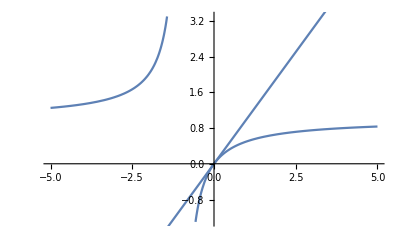

```mathematica
Show[Plot[rho/(1+rho),{rho,-5,5}],Plot[rho,{rho,-5,10}]]
```

```mathematica
(*For the region of the parameter space we are interested in (rho>-1) the condition m>rho is thus sufficient for the existence of a positive equilibrium. Intuitively it makes sense: if migration is so important that microbes migrate out of the host faster than they replicate in it (m>rH) then the exponential growth never truly has the time to kick in and competition is efficient everywhere despite formally existing only in the host. If migration is smaller than replication though, we DO have dnH/dt always positive, and a population that explodes in the environment.*)
```

```mathematica
popFinal[rho_,m_]:=nEV[rho,m]+nHV[rho,m]
```

```mathematica
FullSimplify[D[popFinal[rho,m],rho]]
```

(m (m+2 m^2-rho))/(k (m-rho)^3)

```mathematica
DLDRHO[rho_,m_]:=(m (m+2 m^2-rho))/(k (m-rho)^3)
```

```mathematica
FullSimplify[D[popFinal[rho,m],m]]
```

(rho (-m+rho-3 m rho+rho^2))/(k (m-rho)^3)

```mathematica
DLDM[rho_,m_]:=(rho (-m+rho-3 m rho+rho^2))/(k (m-rho)^3)
```

```mathematica
Sol = Refine[Solve[DLDM[rho,m]==-DLDRHO[rho,m],m],m>0&&rho>-1&&rho<1]
```

{{m→1/4 (-1-2 rho-√(1+12 rho+12 rho^2))},{m→1/4 (-1-2 rho+√(1+12 rho+12 rho^2))}}

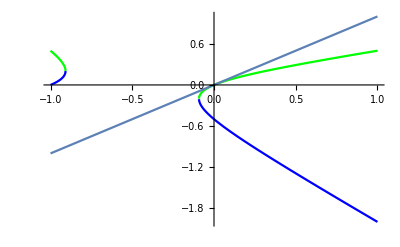

```mathematica
Show[Plot[{m/.Sol[[1]],m/.Sol[[2]]},{rho,-1,1},PlotRange->All,PlotStyle->{Blue,Green}],Plot[rho,{rho,-1,1}]]
```

```mathematica
(*We only keep what is above the m>rho line*)
```

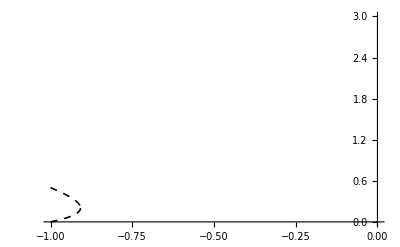

```mathematica
Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}]
```

```mathematica
Sol2=Refine[Solve[DLDM[rho,m]==DLDRHO[rho,m],m],m>0&&rho>-1&&rho<1]
```

{{m→-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{m→-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{m→-1/6-((1-ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1+ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)}}

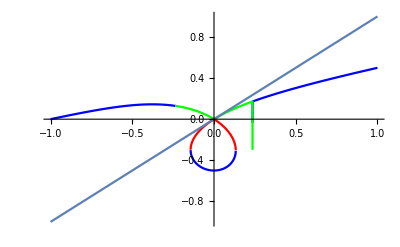

```mathematica
Show[Plot[{m/.Sol2[[1]],m/.Sol2[[2]],m/.Sol2[[3]]},{rho,-1,1},PlotRange->All,PlotStyle->{Blue,Green,Red}],Plot[rho,{rho,-1,1}]]
```

```mathematica
(*We also only keep what is above*)
```

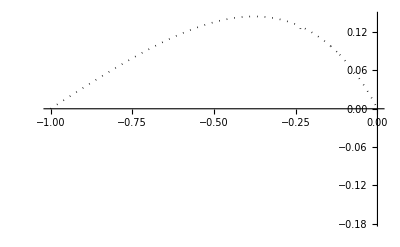

```mathematica
Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]
```

## Parametric maps of λ - Panel A

### Definition of parameters and discretization of the trait space

```mathematica
tmax = 30;
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.025}];
TabM = Table[i,{i,0,2,0.025}];
TabKH ={10^-12,10^-8,10^-4};
Rempl = Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh-> TabKH⟦ikh⟧},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

### Solution on the primary lattice

```mathematica
Sol = Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.Rempl⟦irho,im,ikh⟧/.nE0->NE0/.nH0->NH0,{nW,nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
LambdaTab2 = Table[Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ikh⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ikh⟧⟦1⟧⟦1⟧],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
LambdaTab2Array = Reverse[Table[Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ikh⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ikh⟧⟦1⟧⟦1⟧],{im,1,Length[TabM]},{irho,1,Length[TabRHO]},{ikh,1,Length[TabKH]}]];
```

```mathematica
data = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTab2[[irho,im,ikh]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ikh,1,Length[TabKH]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->TabKH[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->TabKH[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[TabKH]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0/.nH0->NH0,{nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
DMSolGC = Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0/.nH0->NH0,{nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

Part::partw: Part 42 of {{{{re -> 1, rh -> -1., me -> 0.00001, mh -> 0.00001, Kh -> }, <<8>>, {<<5>>}}, <<85>>}, <<40>>} does not exist.

ReplaceAll::reps: {{{{{re -> 1, rh -> -1., me -> 0.00001, mh -> 0.00001, Kh -> }, <<9>>}, <<85>>}, <<40>>}[[42,1,1]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>> in the first argument {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>>.

Part::partw: Part 42 of {{{{re -> 1, rh -> -1., me -> 0.00001, mh -> 0.00001, Kh -> }, <<8>>, {<<5>>}}, <<85>>}, <<40>>} does not exist.

NDSolve::deqn: Equation or list of equations expected instead of {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>> in the first argument {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>>.

Part::partw: Part 42 of {{{{re -> 1, rh -> -1., me -> 0.00001, mh -> 0.00001, Kh -> }, <<8>>, {<<5>>}}, <<85>>}, <<40>>} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>> in the first argument {{nH'[t] == mh nE[t] - me nH[t] + rh nH[t], nH[0] == 0}, {nE'[t] == <<1>>, nE[0] == 1}} /. <<1>>.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmax, NH0,NE0,DRHOSolGC⟦irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ik⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
SensiM = Table[(Biglambda[tmax, NH0,NE0,DMSolGC⟦irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ik⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiRHO = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[irho]][[im]][[ik]]/SensiRHO[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

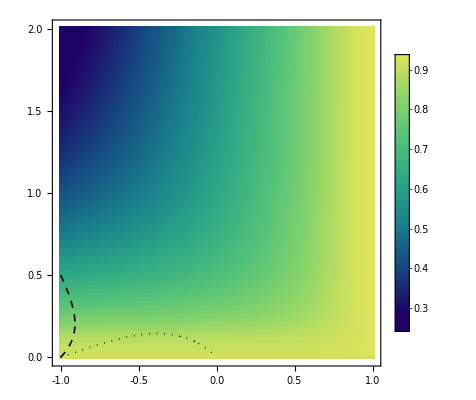
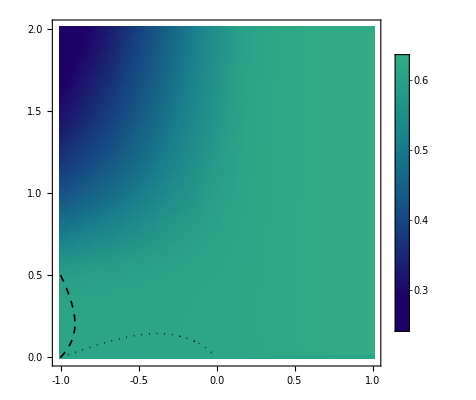
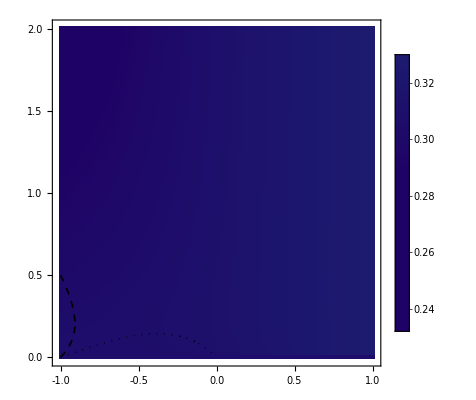

```mathematica
Table[Show[ArrayPlot[LambdaTab2Array[[;;,;;,ikh]],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.29,0.95}]]&),PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{0,"0.0"},{0.5,"0.5"},{1.0,"1.0"},{1.5,1.5},{2.0,"2.0"}},{{-1.0,"-1.0"},{-0.5,-0.5},{0.0,"0.0"},{0.5,0.5},{1.0,"1.0"}},None,None},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold},DataRange->{{-1,1},{0,2}},AspectRatio->1],ListContourPlot[dataSensiRatio[[ikh]],ContourShading->None,Contours->{1},ContourStyle->Directive[Black,Thick],BaseStyle->{FontSize->16}],ListContourPlot[dataSensiRatio[[ikh]],ContourShading->None,Contours->{-1},ContourStyle->Directive[Black,Thick,Dashed],BaseStyle->{FontSize->16},PlotRange->All],Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}],Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]],{ikh,1,Length[TabKH]}]
```

## Panel C - Kh=10^-8 fixed, effect of time, nE0 = 0, nH0 = 1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {5,10,15,20,30,40,50,60};
NE0B = 0;
NH0B = 1;
RE = 1;
Listk={10^-8};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM = Flatten[{0,0.001,0.01,Table[i,{i,0.02,2,0.025}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

#### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

### Plot

```mathematica
listcolor=Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]
```

{RGBColor[0.122103, 0.00901808, 0.39826],RGBColor[0.08943771428571429, 0.24098401142857143, 0.49412457142857147],RGBColor[0.09378314285714286, 0.43570714285714285, 0.5372898571428572],RGBColor[0.14216071428571428, 0.5862125714285714, 0.5369255714285714],RGBColor[0.24151514285714284, 0.699388, 0.505396],RGBColor[0.3987782857142857, 0.7844317142857143, 0.45559771428571433],RGBColor[0.6208947142857143, 0.8482312857142857, 0.39989485714285716],RGBColor[0.914809, 0.897673, 0.350652]}

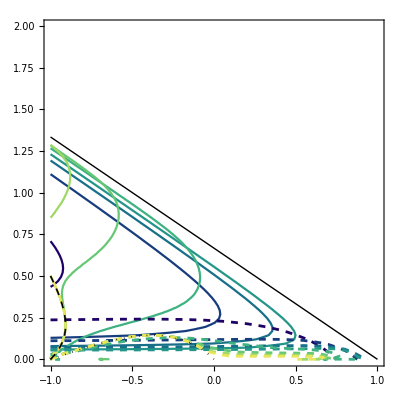

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All,LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.005],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}],Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]]
```

## Panel E - tmax=30 fixed, effect of Kh, nE0 = 0, nH0 = 1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {30};
NE0B = 0;
NH0B = 1;
RE = 1;
Listk=10^-{12,11,10,9,8,7,6,5,4};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM = Table[i,{i,0,2,0.025}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

#### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

### Plot

```mathematica
listcolor=Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[Listk]-1)}]
```

{RGBColor[0.122103, 0.00901808, 0.39826],RGBColor[0.093520875, 0.21198827, 0.48214150000000006],RGBColor[0.09084624999999999, 0.38888849999999997, 0.5291335],RGBColor[0.11715099999999999, 0.53666725, 0.54324775],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.29102125, 0.73472425, 0.48807100000000003],RGBColor[0.4507175, 0.8010995000000001, 0.441349],RGBColor[0.657634, 0.8544115000000001, 0.3937395],RGBColor[0.914809, 0.897673, 0.350652]}

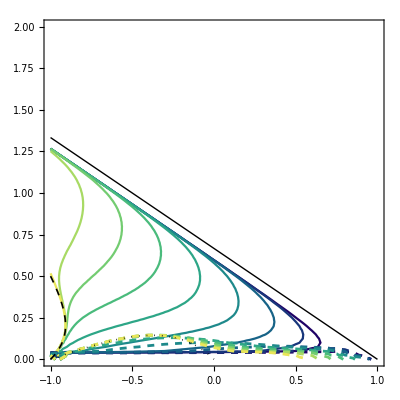

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,ikh]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ikh]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,2}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{ikh,1,Length[Listk]}],Table[ListContourPlot[dataSensiRatio[[1,ikh]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ikh]],Thickness[0.005],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{ikh,1,Length[Listk]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}],Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]]
```

## Panel B - nE0 = 1 and nH0 = 0, k=10^-8 fixed, varying time

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {0.1,1,2,5,20,25,30,35,40,45,50,55};
NE0B = 1;
NH0B = 0;
RE = 1;
Listk={10^-8};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM = Flatten[{0,0.01,Table[i,{i,0.025,2,0.025}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

```mathematica
listcolor=Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[tmaxB]-1)}]
```

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.5972463636363636, 0.044445454545454545, 0.011508072727272728],RGBColor[0.7257507272727273, 0.08889090909090909, 0.007192545454545455],RGBColor[0.8355684545454546, 0.14530281818181817, 0.006531554545454546],RGBColor[0.8893262727272727, 0.23761409090909089, 0.01683417272727273],RGBColor[0.943084090909091, 0.3299253636363636, 0.027136790909090915],RGBColor[0.9754242727272727, 0.4253260909090909, 0.04099406363636364],RGBColor[0.9863468181818182, 0.5238162727272727, 0.058405990909090905],RGBColor[0.9972693636363636, 0.6223064545454545, 0.07581791818181818],RGBColor[1., 0.6941648181818182, 0.0929302],RGBColor[1., 0.7571459090909092, 0.1099426],RGBColor[1., 0.820127, 0.126955]}

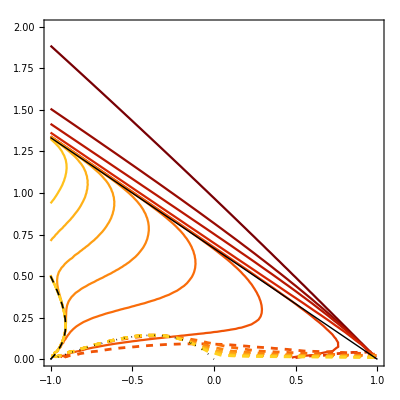

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,2}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.005],Opacity[1],Dashed],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}],Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]]
```

## Panel D - nE0 = 1 and nH0 = 0, tmax=30 fixed, varying k

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {30};
NE0B = 1;
NH0B = 0;
RE = 1;
Listk=10^-{12,11,10,9,8,7,6,5,4};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM = Flatten[{Table[i,{i,0.,0.1,0.01}],Table[i,{i,0.15,2,0.025}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

```mathematica
listcolor=Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[Listk]-1)}]
```

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6454355, 0.0611125, 0.00988975],RGBColor[0.822129, 0.122225, 0.0039559],RGBColor[0.896046, 0.24915299999999999, 0.018122],RGBColor[0.969963, 0.376081, 0.0322881],RGBColor[0.9849815, 0.511505, 0.0562295],RGBColor[1., 0.646929, 0.0801709],RGBColor[1., 0.733528, 0.10356295000000001],RGBColor[1., 0.820127, 0.126955]}

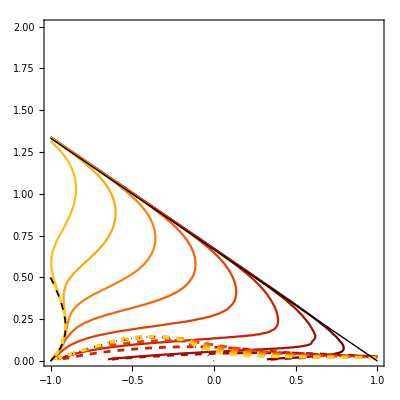

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,ik]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All,LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{ik,1,Length[Listk]}],Table[ListContourPlot[dataSensiRatio[[1,ik]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.005],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{ik,1,Length[Listk]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[{1/4 (-1-2 rho-√(1+12 rho+12 rho^2)),1/4 (-1-2 rho+√(1+12 rho+12 rho^2))},{rho,-1,0},PlotRange->{{-1,0},{0,3}},PlotStyle->{Directive[Black,Dashed,Thickness[0.003]],Directive[Black,Dashed,Thickness[0.003]]}],Plot[{-1/6+(-1+18 rho^2)/(6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))-1/6 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3),-1/6-((1+ⅈ √3) (-1+18 rho^2))/(12 (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3))+1/12 (1-ⅈ √3) (1-81 rho^2-54 rho^3+3 √3 √(-4 rho^2-4 rho^3+207 rho^4+324 rho^5+324 rho^6))^(1/3)},{rho,-1,0},PlotStyle->{Directive[Black,Dotted,Thickness[0.003]],Directive[Black,Dotted,Thickness[0.003]]}]]
```